```mathematica
Impulzna motnja
```

```mathematica
Podatki
```

```mathematica
m=534.0;
k=19400;
d=4900;
F0=1800;
t0=2;
g=9.81;
```

```mathematica
Izracun lastne nedusene in dusene krozne frekvence
```

```mathematica
ω0=√(k/m);
δ=d/(2 m ω0);
ωd=ω0 √(1-δ^2);
```

```mathematica
Prvi del F1(t)
```

```mathematica
x1=Integrate[F0/m 1/ωd Sin[ωd(t-τ)] ⅇ^(-δ ω0 (t-τ)),{τ,0,t}];
x2=Integrate[F0/m 1/ωd Sin[ωd(t-τ)] ⅇ^(-δ ω0 (t-τ)),{τ,0,t0}];
```

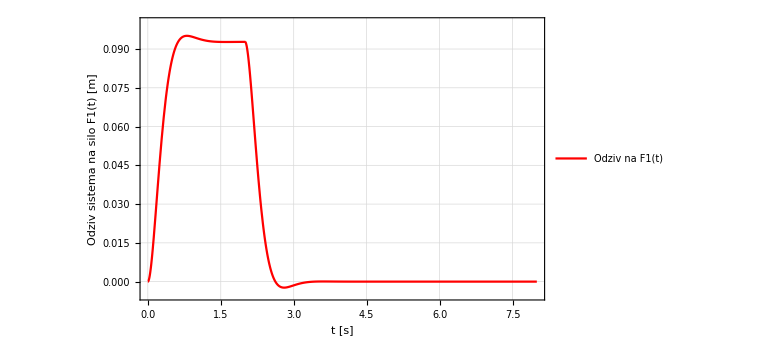

```mathematica
A=Plot[x1,{t,0,t0},PlotRange->{{0,t0},{-0.02,0.1}},Frame->True,FrameLabel->{"t [s]","Odziv sistema na silo F1(t) [m]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->Large,PlotStyle->Red,PlotLegends->{"Odziv na F1(t)"}];
B=Plot[x2,{t,t0,4t0},PlotRange->{{t0,4t0},{-0.02,0.1}},PlotStyle->Red];
Odziv1=Show[A,B,PlotRange->{{0,4t0},{-0.005,0.1}}]
```

```mathematica
(*Export["Graf_odziv_F1.pdf",Odziv1];
SystemOpen["Graf_odziv_F1.pdf"];*)
```

```mathematica
Drugi del F2(t)
```

```mathematica
x1=Integrate[F0/m ⅇ^(-τ/t0) 1/ωd ⅇ^(-δ ω0 (t-τ)) Sin[ωd(t-τ)],{τ,0,t}];
x2=Integrate[F0/m ⅇ^(-τ/t0) 1/ωd ⅇ^(-δ ω0 (t-τ)) Sin[ωd(t-τ)],{τ,0,t0}];
```

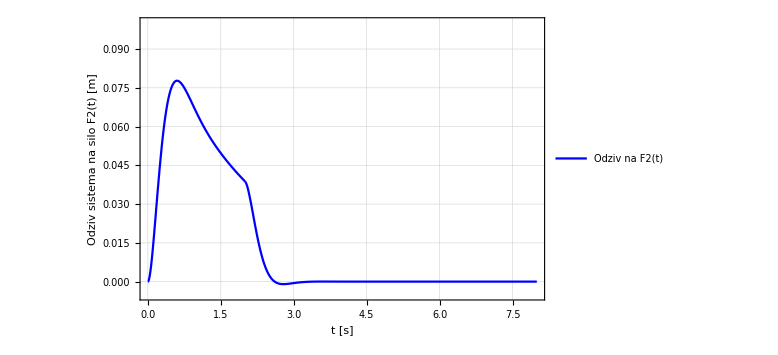

```mathematica
A=Plot[x1,{t,0,t0},PlotRange->{{0,t0},{-0.02,0.1}},Frame->True,FrameLabel->{"t [s]","Odziv sistema na silo F2(t) [m]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->Large,PlotStyle->Blue,PlotLegends->{"Odziv na F2(t)"}];
B=Plot[x2,{t,t0,4t0},PlotRange->{{t0,4t0},{-0.02,0.1}},PlotStyle->Blue];
Odziv2=Show[A,B,PlotRange->{{0,4t0},{-0.005,0.1}}]
```

```mathematica
(*Export["Graf_odziv_F2.pdf",Odziv2];
SystemOpen["Graf_odziv_F2.pdf"];*)
```

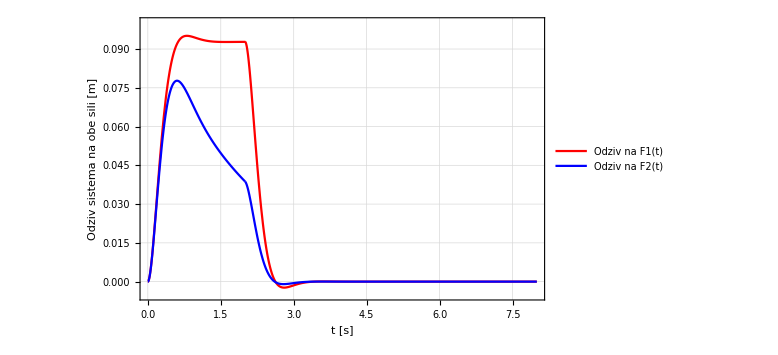

```mathematica
Skupno=Show[Odziv1,Odziv2,FrameLabel->{"t [s]","Odziv sistema na obe sili [m]"}]
```

```mathematica
(*Export["Graf_odziv_skupno.pdf",Skupno];
SystemOpen["Graf_odziv_skupno.pdf"];*)
```

```mathematica
++++++++++++++++++++++Primerjav a parametrov pri F1(t)+++++++++++++
```

```mathematica
Clear[ω0,k,m,d,δ,ωd,x1,x2,t,t0,F0];
```

```mathematica
ω0[k_,m_]=√(k/m);
δ[d_,m_]=d/(2 m ω0);
ωd[k_,d_,m_]=ω0[k,m] √(1-(δ[d,m])^2);
x1[t_,m_,k_,d_,F0_]=Integrate[F0/m 1/ωd[k,d,m] Sin[ωd[k,d,m](t-τ)]Exp[-δ[d,m]ω0[k,m](t-τ)],{τ,0,t}]/.ω0->√(k/m);
x2[t_,m_,k_,d_,F0_]=Integrate[F0/m 1/ωd[k,d,m] Sin[ωd[k,d,m](t-τ)]Exp[-δ[d,m]ω0[k,m](t-τ)],{τ,0,t0}]/.ω0->√(k/m);
```

```mathematica
t0=2;
skupna[t_,m_,k_,d_,F0_]=Piecewise[{{x1[t,m,k,d,F0],0≤t<t0},{x2[t,m,k,d,F0],t≥t0}}];
```

```mathematica
Manipulate[Plot[skupna[t,m,k,d,F0],{t,0,4t0},PlotRange->{{0,4 t0},{-0.02,0.15}},Frame->True,FrameLabel->{"t [s]","Odziv sistema na silo F1(t) [m]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->Large,PlotStyle->Red,PlotLegends->{"Odziv na F1(t)"}],{{m,534},1,534 2},{{k,19400},1,19400 2},{{d,4900},0,4900 2},{{F0,1800},0,1800 1.5}]
```